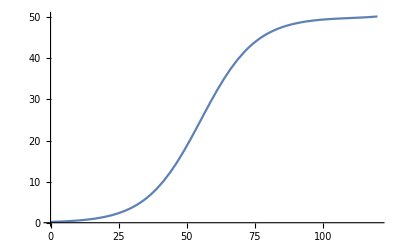

```mathematica
pars = {r-> 0.1, Ca -> 50, α -> 0.002};
sys = {
D[y[t], t] == r* y[t] *(1 - y[t]/Ca)
};
vars = {y};
init= {y[0] == 0.2};
sol = NDSolve[Join[sys, init]/.pars, vars, {t, 0, 100}];
Plot[Evaluate[y[t]/.sol], {t, 0, 120}, PlotRange->All]
```

```mathematica
eqEc[Ec_,Z_]:=Ec * (rE - rE/cE Ec + Subscript[α, EZ]*Z);
eqZ[Ec_,Z_]:=Z * (rZ - rZ/cZ Z + Subscript[α, ZE]*Ec);
eql = Solve[{eqEc[Ec, Z] == 0.0, eqZ[Ec, Z] == 0.0}, {Ec, Z}]
jacob = D[{eqEc[Ec, Z], eqZ[Ec, Z]}, {{Ec, Z}}];
jacob // MatrixForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ec→0.,Z→1. cZ},{Ec→-(1. (1. cE rE rZ+1. cE cZ rZ α_EZ))/(-1. rE rZ+cE cZ α_EZ α_ZE),Z→-(1. (1. cZ rE rZ+1. cE cZ rE α_ZE))/(-1. rE rZ+cE cZ α_EZ α_ZE)},{Ec→0.,Z→0.},{Ec→1. cE,Z→0.}}

(rE-(2 Ec rE)/cE+Z α_EZ | Ec α_EZ
Z α_ZE | rZ-(2 rZ Z)/cZ+Ec α_ZE)

```mathematica
Table[Eigenvalues[jacob/.eql[[i]]], {i, {1, 3, 4}}]
```

{{-1. rZ,rE+1. cZ α_EZ},{rE,rZ},{-1. rE,rZ+1. cE α_ZE}}

Eigenvalues of equilibria with competitive exclusion are always real => monotonically converge or diverge

```mathematica
pars = {rE-> 0.01, cE -> 0.4, rZ->0.02, cZ -> 0.2, Subscript[α, EZ] ->0.0, Subscript[α, ZE] -> 0.0};
eql = NSolve[{eqEc[Ec, Z] == 0.0, eqZ[Ec, Z] == 0.0}/.pars, {Ec, Z}]
jacob = D[{eqEc[Ec, Z], eqZ[Ec, Z]}/.pars, {{Ec, Z}}]
Table[Eigenvalues[jacob/.eql[[i]]], {i, 1, 4}]
```

{{Ec→0.,Z→0.},{Ec→0.4,Z→0.},{Ec→0.,Z→0.2},{Ec→0.4,Z→0.2}}

{{0.01-0.05 Ec,0},{0,0.02-0.2 Z}}

{{0.02,0.01},{0.02,-0.01},{-0.02,0.01},{-0.02,-0.01}}

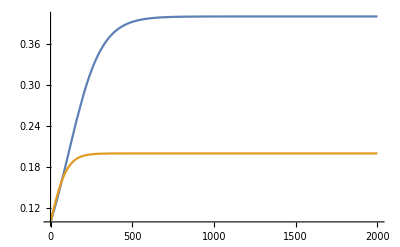

```mathematica
sys = {D[Ec[t], t] == eqEc[Ec[t], Z[t]], D[Z[t], t] == eqZ[Ec[t], Z[t]]};
vars = {Ec[t], Z[t]};
tmin = 0.0;
tmax = 2000;
init = {Ec[tmin] == 0.1, Z[tmin] == 0.1};
solution = NDSolve[{sys, init}/.pars, vars, {t, tmin, tmax}];
Plot[Evaluate[{Ec[t], Z[t]}/.solution], {t, tmin, tmax}, PlotRange->{All, All}]
```

```mathematica
DSolve[d'[t] == -k*d[t], d[t], t]
```

{{d[t]→ⅇ^(-k t) C[1]}}

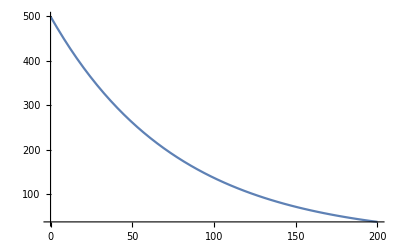

{136.266}

```mathematica
tmax = 200;
solD = NDSolve[{d'[t] == -k*d[t], d[0]==500}/.{k-> 0.013}, d[t], {t, 0, tmax}];
Plot[Evaluate[d[t]/.solD], {t, 0, tmax}, PlotRange->All]
d[t]/.solD/.{t->100}
```

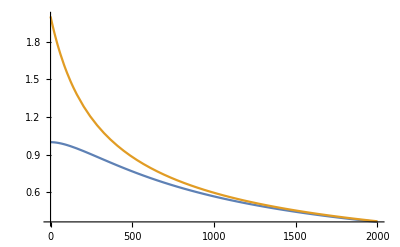

```mathematica
eqX1[X1_,X2_]:=X1 * (r1 - r1/C1 X1 + a12*X2-d1);
eqX2[X1_,X2_]:=X2 * (r2 - r2/C2 X2 + a21*X1-d2);
(*eql = NSolve[{eqX1[X1, X2] == 0.0, eqX2[X1, X2] == 0.0}, {X1, X2}]
jacob = D[{eqX1[X1, X2], eqX2[X1, X2]}, {{X1, X2}}]*)
sys = {D[X1[t], t] == eqX1[X1[t], X2[t]], D[X2[t], t] == eqX2[X1[t], X2[t]]};
vars = {X1[t], X2[t]};
tmin = 0.0;
tmax = 2000;
pars = {r1-> 0.1, C1 -> 50, r2->0.2, C2 -> 100, a12 -> 0.001, a21 -> 0.001, d1->0.1, d2->0.2};
init = {X1[tmin] == 1, X2[tmin] == 2};
solution = NDSolve[Join[sys, init]/.pars, vars, {t, tmin, tmax}];
Plot[Evaluate[{X1[t], X2[t]}/.solution], {t, tmin, tmax}, PlotRange->{All, All}]
```